```mathematica
λ=500*10^(-9);
z=5*10^(0);
intensity[x_,y_,diam_]:=(2*λ *z*BesselJ[1,π*Sqrt[x^2+y^2]*diam/(λ*z)]/π*Sqrt[x^2+y^2]*diam)^2
```

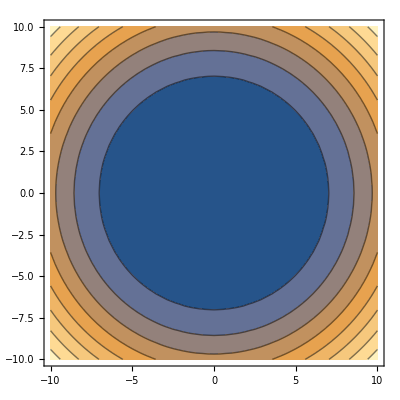

```mathematica
ContourPlot[intensity[x,y,0.001],{x,-10,10},{y,-10,10}]
```

```mathematica
Manipulate[ContourPlot[intensity[x,y,diam],{x,-0.1,0.1},{y,-0.1,0.1}],{diam,0,0.01}]
```